# Mathematica Lab 1-Properties Fourier Series Representation

## Property-First Difference of a Discrete-Time Periodic Signal (with general explanations) *SCIMATH301 - Signals & Systems* *Joanikij Chulev* *22.09.2022*

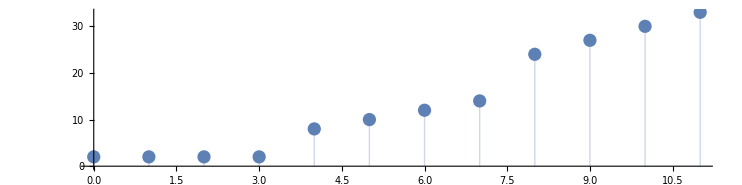

```mathematica
(* This defines one period of the periodic signal x[n]: *)
P=12;
x[n_Integer]:=Piecewise[{{2,0≤Mod[n,P]<4},{2*Mod[n,P],4≤Mod[n,P]<8},{3*Mod[n,P],8≤Mod[n,P]≤11}}];
(* This defines the period of the signal: *)(* P is the notation for big N *)
(* This plots the single period of the signal: *)
ListPlot[Table[{n,x[n]},{n,0,11}],Filling->Axis,AspectRatio->1/4]
```

1/12 (2+2 ⅇ^(-1/6 ⅈ k π)+2 ⅇ^(-1/3 ⅈ k π)+2 ⅇ^(-1/2 ⅈ k π)+8 ⅇ^(-2/3 ⅈ k π)+10 ⅇ^(-5/6 ⅈ k π)+12 ⅇ^(-ⅈ k π)+14 ⅇ^(-7/6 ⅈ k π)+24 ⅇ^(-4/3 ⅈ k π)+27 ⅇ^(-3/2 ⅈ k π)+30 ⅇ^(-5/3 ⅈ k π)+33 ⅇ^(-11/6 ⅈ k π))

0 | 83/6
1 | -5/6+11/(8 √3)+ⅈ (85/24+11/(2 √3))
2 | -35/24+(13 ⅈ √3)/8
3 | -5/6+(5 ⅈ)/6
4 | -37/24+(5 ⅈ √3)/8
5 | -5/6-11/(8 √3)+ⅈ (85/24-11/(2 √3))
6 | -5/6
7 | -5/6-11/(8 √3)+ⅈ (-85/24+11/(2 √3))
8 | -37/24-(5 ⅈ √3)/8
9 | -5/6-(5 ⅈ)/6
10 | -35/24-(13 ⅈ √3)/8
11 | -5/6+11/(8 √3)+ⅈ (-85/24-11/(2 √3))

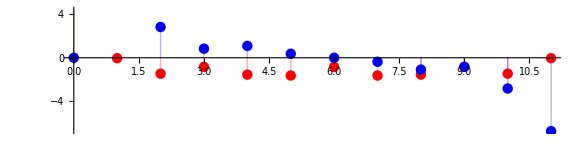

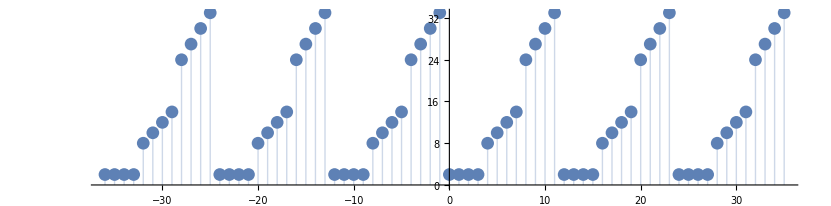

```mathematica
(* This computes the Fourier Series coefficients: *)
a[k_Integer]=1/P Total[Table[x[n]Exp[-ⅉ k (2π)/P n],{n,0,P-1}]]
(* These are all the ak's: *)
Grid[Table[{k,ComplexExpand[a[k]]},{k,0,P-1}],Frame->All]
(* This plots the real and imaginary parts of the ak's: *)
Pak=ListPlot[{Table[{k,Re[a[k]]},{k,0,P-1}],Table[{k,Im[a[k]]},{k,0,P-1}]},Filling->Axis,PlotStyle->{Red,Blue},AspectRatio->1/4]
(* This synthesizes the discrete-time signal x[n]: *)
xsyntesized[n_Integer]:=Total[Table[a[k]Exp[ⅉ k (2π)/12 n],{k,0,11}]]
(* This Plots the synthesized discrete-time signal x[n]: *)
Px=ListPlot[Table[{n,ComplexExpand[xsyntesized[n]]},{n,-36,35}],Filling->Axis,AspectRatio->1/4]
```

```mathematica
(* THIS IMPLEMENTS THE FIRST DIFFERENCE *)
y[n_]:=x[n]-x[n-1]; (*For example lets take value n=5. Than y(n)=x(5)-x(4)=5*2-4*2=2 thus y(n)=2. We can see that in the graph !)
```

1/12 (-31+6 ⅇ^(-2/3 ⅈ k π)+2 ⅇ^(-5/6 ⅈ k π)+2 ⅇ^(-ⅈ k π)+2 ⅇ^(-7/6 ⅈ k π)+10 ⅇ^(-4/3 ⅈ k π)+3 ⅇ^(-3/2 ⅈ k π)+3 ⅇ^(-5/3 ⅈ k π)+3 ⅇ^(-11/6 ⅈ k π))

0 | 0
1 | -79/24-1/(8 √3)+ⅈ (3/8+7/(8 √3))
2 | -19/6+ⅈ/(4 √3)
3 | -5/3
4 | -13/4+ⅈ/(2 √3)
5 | -79/24+1/(8 √3)+ⅈ (3/8-7/(8 √3))
6 | -5/3
7 | -79/24+1/(8 √3)+ⅈ (-3/8+7/(8 √3))
8 | -13/4-ⅈ/(2 √3)
9 | -5/3
10 | -19/6-ⅈ/(4 √3)
11 | -79/24-1/(8 √3)+ⅈ (-3/8-7/(8 √3))

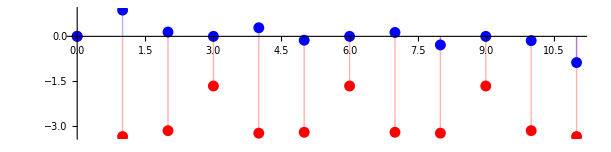

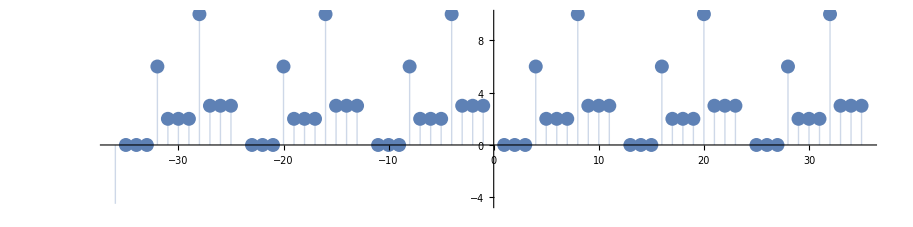

```mathematica
(* This computes the Fourier Series coefficients (the transformation is included below): : *)
b[k_Integer]=1/P Total[Table[y[n]Exp[-ⅉ k (2π)/P n],{n,0,P-1}]]
(* These are all the ak's: *)
Grid[Table[{k,ComplexExpand[b[k]]},{k,0,P-1}],Frame->All]
(* This plots the real and imaginary parts of the ak's: *)
Pbk=ListPlot[{Table[{k,Re[b[k]]},{k,0,P-1}],Table[{k,Im[b[k]]},{k,0,P-1}]},Filling->Axis,PlotStyle->{Red,Blue},AspectRatio->1/4]
(* This synthesizes the discrete-time signal x[n-n0] (the transformation is included below): *)
ysyntesized[n_Integer ]:=Total[Table[b[k]Exp[ⅉ k (2π)/12 n],{k,0,11}]]
(* This Plots the synthesized discrete-time signal x[n] *)
Py=ListPlot[Table[{n,ComplexExpand[ysyntesized[n]]},{n,-36,35}],Filling->Axis,AspectRatio->1/4]
```

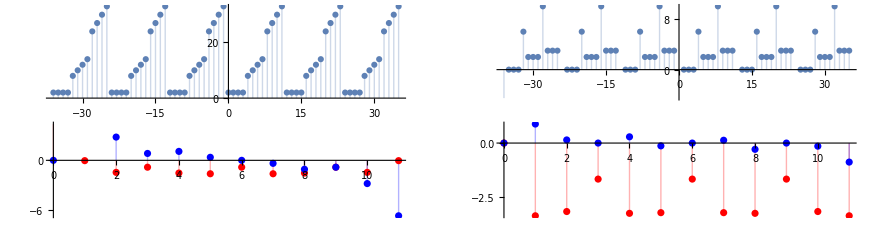

```mathematica
(* This shows all plots in one overview: *)
GraphicsGrid[{{Px,Py},{Pak,Pbk}},Frame->True]
```